## Problem Set 15 SOLUTION — The Mug Breakage Problem — With a Gamma Distribution Prior — ! Was numbered Problem Set 14 !

## 1. Tabulating the Gamma Function

This whole thing that we are looking at,

P(a)=β^α/(Γ(α))a^(α-1)e^-βa,

I have been calling  “the gamma function,” and that is incorrect.  The thing in the denominator that is needed to normalize this function is what is actually called “the gamma function.” To disambiguate this, I will try to be better and do what statisticians do which is to call the whole thing “the gamma distribution” and then what is in the denominator is “the gamma function.”

Here is a graph of the gamma function (the thing in the denominator):

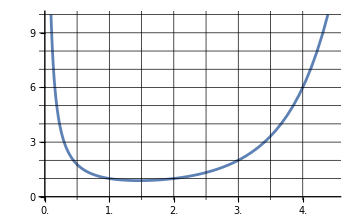

```mathematica
Plot[Gamma[x],{x, 0, 4.5},PlotRange->{{0.0,4.5},{0,10}}, GridLines->{Range[0,4,0.5],Range[0,10,1]}, GridLinesStyle->Directive[Black],Ticks->{Range[0.0,4.5,0.5],Range[0,10,1]}]
```

(a) Examining the graph on the previous page, please write down, what is

Γ(1)= 1
Γ(2)= 1
Γ(3)= 2
Γ(4)= 6

(b) Γ(n+1)= n!

## 2. Exploring the Gamma Distribution

(a) Coming back to the gamma distribution

P(a)=β^α/(Γ(α))a^(α-1)e^-βa

Simplify this for the special case α=2 and β=3:

P(a)=3^2/(Γ(2))a^(2-1)e^(-3a)=9a e^(-3a)

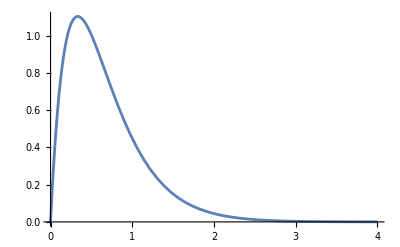

```mathematica
gamma[a_,α_,β_]:=β^α/Gamma[α] a^(α-1)Exp[-βa];
Plot[gamma[a,2,3],{a,0,4}]
```

(b) The junk out front of the function you found is just there to normalize the function to have total area 1 and it might be plausible that the function above indeed has area 1.If I had asked you to simplify the exact same function, except without the junk out front, you’d be simplifying  Q(a)=a^(α-1)e^-βa. Please simplify that for the same special case, α=2 and β=3:

 Q(a)=a e^(-3a)

(c) What is the area under the curve of Q(a)?

The 9 was left off the front, so this curve must have area 1/9.

(d)  Is (Q(a))/(∫_0^∞ Q(b)db) proportional to Q(a)? Yes, of course. They only differ by a constant factor of ∫_0^∞ Q(b)db

(e) What is the area under the curve of the function (Q(a))/(∫_0^∞ Q(b)db)? It is 1. Because the bottom is the area under the curve of Q(a).

## 3. Some Likelihoods

We observe the kitchen for two weeks and see 4 mugs broken in one week and then 1 mug broken in the next.

(a) Write down the likelihood of having n=4 mugs broken in the first week.

(a^4 e^-a)/(4!)=(a^4 e^-a)/24

(b) Repeat, but with n=1 mug for the second week.

(a e^-a)/(1!)=a e^-a

(c) Take the product of what you got in (a) and (b).

P(data|a)=(a^5 e^(-2a))/24

## 4. The Posterior

In 2(a) you wrote down the prior, P(a). In 3(c) you wrote down the posterior, P(data|a).

By Bayes theorem, you know that the posterior is proportional to  P(data|a)P(a). The proportionality constant is something I often call “denominator” and it is

∫_0^∞ P(data|b)P(b)db

What Bayes theorem says is

P(a|data)=(P(data|a)P(a))/(∫_0^∞ P(data|b)P(b)db)

(a) Just ignore the denominator for a minute. It doesn’t depend on a, so it only changes the overall vertical scale of the function. Pretend for just a minute that it isn’t there, and if it weren’t then simplify:

P_(pretend version)(a|data)=P(data|a)P(a)=(a^5 e^(-2a))/24 9a e^(-3a)

Here’s another thing you can do. Just get rid of the 9  in the formula you just wrote by scratching it out, since we are throwing away proportionality factors.

AND I SHOULD HAVE SUGGESTED LEAVING OFF THE 24 AT THIS STEP TOO, IN WHICH CASE:

P_(pretend version)(a|data)=a^6 e^(-5a)

(b) What gamma distribution is this proportional to? Once you have figured that out. Write down the whole gamma distribution:

We are comparing with  P_(pretend version)(a|data) with P(a)=β^α/(Γ(α))a^(α-1)e^-βa. We see

α_posterior = 7

β_posterior= 5

P_(complete version)(a|data)=5^7/(Γ(7))a^6 e^(-5a)

(c) Remember how Jacob described it as “greedy” to use the formulas like 11.20 and 11.22 on p. 165 of Donovan and Mickey? Well, you have those formulas for the gamma distribution. Donovan and Mickey use n to mean the number of weeks of data, and they use ∑_(i=1)^n x_i to refer to the total number of mugs broken in those weeks. Can you double check that with n=2 and the total number of mugs broken = 5 that the α_posterior and β_posterior computed with their formulas agrees with what you got above? Greedy method:

α_posterior=2+4 + 1=7

β_posterior=3+2=5

(d) Hopefully the cross-check in (c) worked out. Finally, if you haven’t already, can you use what you learned about Γ(α) in Problem 1 to finish simplifying the real posterior with all the necessary normalization constants:

P(a|data)=5^7/(6!)a^6 e^(-5a)=78125/720 a^6 e^(-5a)=15625/144 a^6 e^(-5a)